## Importing Libraries

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
```

```mathematica
$ContextPath
```

{XMPTools`,JLink`,WolframAlphaClient`,StreamingLoader`,InterpreterLoader`,IconizeLoader`,HTTPHandlingLoader`,CloudObjectLoader`,PacletManager`,System`,Global`}

```mathematica
<<ResistorProject`
```

prepareImage::shdw: Symbol prepareImage appears in multiple contexts {ResistorProject`,Global`}; definitions in context ResistorProject` may shadow or be shadowed by other definitions.

## Import images

```mathematica
imagesPath = NotebookDirectory[] <> "ResistorProject/Assets/Images/";
dataPath = NotebookDirectory[] <> "ResistorProject/Assets/Data/";
```

```mathematica
importByType [type_String] :=
	Map[
		Import,
		FileNames["*.jpg", imagesPath <> type <> "/"]
	];
```

```mathematica
cutSampleResistor[image_] := Module[
	{comp, div, centers, recPos, dim, img},
	dim = ImageDimensions[image];
	If[dim[[1]] > dim[[2]],
		img = ImageRotate[image],
		img = image
	];
	comp = MorphologicalComponents[
		DeleteSmallComponents[
			ColorNegate @ Binarize[
				ColorConvert[img,"Grayscale"] ^(1/5.2)
			]
		]
	];
	recPos = Values[ComponentMeasurements[comp, "MinimalBoundingBox"]];
	div = Map[Mean,Partition[Sort @ Flatten[recPos[[All, All, 2]]],2]];
	div = Take[div, {2, -2}];
	centers = Table[Mean[{div[[x]], div[[x+1]]}], {x, 1, Length[div] - 1, 2}];
	centers = Flatten[{1, centers, -1}];
		Table[
			ImageTake[img, {-centers[[x+1]], -centers[[x]]}, {1, -1}],
			{x, 1, Length[centers] - 1}
		]
]
```

```mathematica
equalizeSize[image_] := Module[
{width, height, img},
	width = 1400;
	height = 350;
	img = ImageResize[image, {Automatic, height}];
	img = ImageCrop[img, {width, height}, Padding->"Fixed"]
]
```

```mathematica
(*types = {"220KOhm", "4.7KOhm", "10Ohm"};
catImages = Flatten @ Map[ 
	ReplaceAll[importByType[#], x_Image:>{x->#}]&,
	types
];*)

produceData[types_] := 
	Flatten @ Table[
		Module[
			{pictures},
			pictures = importByType[types[[x]]];
			pictures = Flatten[Map[cutSampleResistor,pictures]];
			pictures = Map[RemoveAlphaChannel[prepareImage[equalizeSize[#]]]&, pictures];
			pictures = ReplaceAll[pictures, a_Image:>(a->types[[x]])]
		],
		{x, 1, Length[types]}
	]
```

```mathematica
SetDirectory[dataPath];
types = Select[Map[dataPath <> #&,FileNames[]],DirectoryQ];
If [Length[types] == 0,
	Module[
		{imageNumber, path},
		SetDirectory[imagesPath];
		imageNumber = 0;
		types = FileNames[];
		data = produceData[types];
		KeyValueMap[
			Module[
				{folderPath},
				folderPath = dataPath <> #2 <> "/";
				If[!DirectoryQ[folderPath], CreateDirectory[folderPath]];
				Export[folderPath <> "/data" <> ToString[imageNumber++] <> ".png", #1]
			]&,
			Association[data]
		]
	],
	types = Map[StringDrop[#,StringLength[dataPath]]&, types];
	f[type_] := Map[
		Import[#]->type&,
		Join[FileNames["*.png", dataPath <> type <> "/"], FileNames["*.jpg", dataPath <> type <> "/"]]
	];
	data = Flatten @ Map[
		f,
		types
	]
];
ResetDirectory[];
```

## Process

```mathematica
data
```

```mathematica
Length[data]
```

412

```mathematica
dataset = RandomSample[data];
```

```mathematica
trainingset = dataset[[;;300]];
testset=dataset[[301;;]];
c = Classify[trainingset, FeatureExtractor->"PixelVector",
Method->"NeuralNetwork",
PerformanceGoal->"Quality"
]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[c,testset[[;;30]]];
```

Part::take: Cannot take positions 1 through 30 in testset.

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of c.

```mathematica
cm["Accuracy"]
```

0.666667

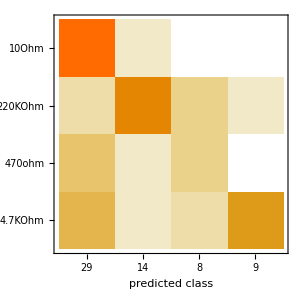

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
c[-Graphics-,"Probabilities"]
```

<|10Ohm→0.369277,220KOhm→0.0134079,4.7KOhm→0.617315|>